## Some formulae

```mathematica
CalculateInOutFormulaKeep[g_]:=CalculateInOutFormulaKeep[g,VertexList[g]]
```

```mathematica
LetterAssoc[n_]:=Table[k->Symbol[MyLetter[k]],{k,n}]
```

```mathematica
LetterAssoc[10]
```

{1→a,2→b,3→c,4→d,5→e,6→f,7→g,8→h,9→i,10→j}

```mathematica
MakeSym[s1_,s2_]:=Block[{n1=If[StringQ[s1],s1, SymbolName[s1]],n2=If[StringQ[s2],s2,SymbolName[s2]]},
Symbol[StringJoin[Sort[Join[Characters[n1],Characters[n2]]]]]
]
```

```mathematica
MakeSym[ac,bd]
```

abcd

```mathematica
CalculateInOutFormulaKeep[g_,sets_]:=CalculateInOutFormulaKeep[g,sets,LetterAssoc[Length[sets]]]
```

```mathematica
FindFullFormulaWithPrefix[g_,prefix_]:=Fold [Plus,Map[ChangeSymbol[#,prefix]&,FindFullFormula[g]]]
```

```mathematica
FindFullFormulaWithPrefix2 [g_,pref_]:=Block[{res},
(*Print[FindFullFormula[g]];*)
res=Fold [Plus,Table[pref,FindFullFormula[g]]];
(*Print[{"FindFullFormulaWithPrefix2",Graph[g,VertexLabels->"Name"],pref,res}];*)
res
];
```

```mathematica
CalculateInOutFormulaKeep[g_,sets_, repl2_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex, in, out,inVertex,outVertex,
node,
  maxRep, minRep, newRep=Association[repl2],s1,s2},
(*Print[{Graph[g,VertexLabels->"Name"],sets,repl2}];*)
If[VertexCount[g]==0,
Print["VertexCount is zero",g,sets];
Return[1]
];
(* if there is no set, we have a problem *)
If[Length[sets]==0,
Print["No more sets"];
Interrupt[];
];
(* if there is only one set, we are done *)
If[Length[sets]==1,
node=First[sets];
result=Lookup[newRep,node];
Return[result];
];

(* there is more than 1 set : we define in to be the first set, out to be thejoin of the rest *)
in=First[sets];
out=Rest[sets];

(* the whole goal is to remove the  in *)
(* as long as there is an edge between in and out we remove and contract it and recurse *)
edges=EdgeList[g,in<->_];
If[edges≠{},
currentEdge=First[edges];
If[currentEdge[[1]]≠in, 
(* make sure the first vertex is in "in" an dthe second in "out" *)
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
(* the remove is easy, it uses the same vertex set and the same replacement *)
gRemove=EdgeDelete[g,currentEdge];
resRemove=CalculateInOutFormulaKeep[gRemove,sets,repl2];

(* no wthe contract *)
inVertex = currentEdge[[1]];
outVertex = currentEdge[[2]];
s1=Lookup[newRep,inVertex];
s2=Lookup[newRep,outVertex];

minRep=MakeSym[s1,s2];
newRep[inVertex]=minRep;
newRep[outVertex]=minRep;
gContract=GContract[g,currentEdge];
repVertex={inVertex->outVertex}; (* replace the in by the out since we want ot get rid of the in *)
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
resContract=CalculateInOutFormulaKeep[gContract,sets,newRep];
result=resRemove-resContract;
Return[result]
];

(* there are no more edges between in and out so we compute in and recurse with the rest *)
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
resIn=If[VertexCount[gIn]==0,1,Lookup[newRep,First[VertexList[gIn]]]];
resOut=If[VertexCount[gOut]==0,1,CalculateInOutFormulaKeep[gOut,Rest[sets],repl2]];
Return[resIn*resOut]
]
```

```mathematica
CalculateInOutFormulaKeep[CycleGraph[3]]//Factor
```

2 abc-ac b-a bc-ab c+a b c

## Now for the work

```mathematica
ChromaticPolynomial[CycleGraph[3],x]
```

2 x-3 x^2+x^3

```mathematica
2 abc-ac b-ab c+a (-bc+b c)//Expand
```

2 abc-ac b-a bc-ab c+a b c

```mathematica
CalculateInOutFormulaKeep[CycleGraph[4]]//Factor
```

-3 abcd+acd b+ad bc+a bcd+abd c-ad b c+ab cd-a b cd+abc d-a bc d-ab c d+a b c d

```mathematica
CalculateInOutFormulaKeep[CycleGraph[5]]//Factor
```

4 abcde-acde b-ade bc-ae bcd-a bcde-abde c+ade b c-abe cd+ae b cd-ab cde+a b cde-abce d+ae bc d+abe c d-ae b c d-abc de+a bc de+ab c de-a b c de-abcd e+a bcd e+ab cd e-a b cd e+abc d e-a bc d e-ab c d e+a b c d e

```mathematica
CalculateInOutFormulaKeep[CompleteGraph[5]]//Factor//Length
```

52

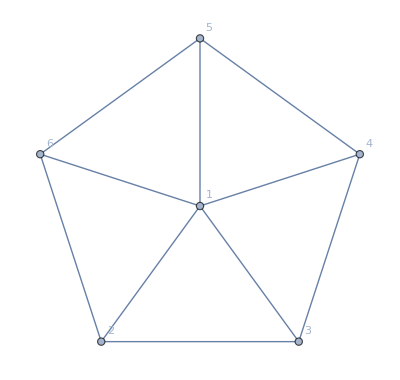

```mathematica
WheelGraph[6,VertexLabels->"Name"]
```

```mathematica
f1=CalculateInOutFormulaKeep[WheelGraph[6]]
```

-30 abcdef+af bcde+ae bcdf+2 ade bcf+4 acde bf-(-abef+ae bf) cd+2 abf cde-(-abcef+ae bcf) d-(-abcef+ace bf) d+c (abdef-ade bf+(-abef+ae bf) d)+4 abcf de+8 abcdf e-4 d (-abcef+abcf e)-2 cd (-abef+abf e)-bcd (-aef+af e)-ad (-bcef+bcf e)-2 acd (-bef+bf e)+2 c (abdef-abf de+d (-abef+abf e))+bc (adef-af de+d (-aef+af e))+c (2 abdef-ade bf-abdf e+ad (-bef+bf e))+ac (bdef-bf de+d (-bef+bf e))-b (-acdef+af cde-cd (-aef+af e)+c (adef-af de+d (-aef+af e)))+8 abcde f-2 d (-abcef+abce f)-cd (-abef+abe f)-bcd (-aef+ae f)-4 abcd (-ef+e f)+c (abdef-abde f+d (-abef+abe f))+bc (adef-ade f+d (-aef+ae f))+c (2 abdef-abdf e-abde f+abd (-ef+e f))+bc (2 adef-adf e-ade f+ad (-ef+e f))+2 abc (def-de f+d (-ef+e f))-b (-acdef+acde f-cd (-aef+ae f)+c (adef-ade f+d (-aef+ae f)))-b (-2 acdef+acdf e+acde f-acd (-ef+e f)+c (2 adef-adf e-ade f+ad (-ef+e f)))-b (-4 acdef+acf de+acdf e-d (-acef+acf e)+2 acde f-d (-acef+ace f)-acd (-ef+e f)+ac (def-de f+d (-ef+e f)))-ab (-cdef+cde f-cd (-ef+e f)+c (def-de f+d (-ef+e f)))+a (4 bcdef-bf cde-bcf de-bcdf e+d (-bcef+bcf e)+cd (-bef+bf e)-c (bdef-bf de+d (-bef+bf e))-bcde f+bcd (-ef+e f)-bc (def-de f+d (-ef+e f))+b (-cdef+cde f-cd (-ef+e f)+c (def-de f+d (-ef+e f))))

```mathematica
ExpressionLattice[exp_]:=Block[{allVars=DeleteDuplicates[ListofVars[exp]],sets, terms, expanded, vars, edges={}},
Print[allVars];
expanded=Expand[exp];
terms=Table[expanded[[k]],{k,Length[expanded]}];
Print[terms];
vars=Map[DeleteDuplicates[ListofVars[#]]&,terms];
Table[If[Length[vars[[from]]]==Length[vars[[to]]]+1&&Length[Intersection[vars[[from]],vars[[to]]]]==Length[vars[[from]]]-1&&Length[vars[[to]]]<Length[vars[[from]]],
AppendTo[edges,DirectedEdge[terms[[from]],terms[[to]]]]
],{from,Length[terms]},{to,Length[terms]}];
Graph[edges,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name", ImageSize->{270,270}, VertexLabelStyle->{Bold,Red}]
]
```

```mathematica
ExpressionLattice[f1]
```

{abcdef,abcde,f,abcdf,e,abcf,de,abf,cde,acde,bf,ade,bcf,ae,bcdf,af,bcde,abcd,ef,acd,bef,ad,bcef,bcd,aef,cd,abef,abe,d,abcef,abce,ace,abc,def,ac,bdef,bc,adef,c,abdef,abde,adf,abdf,abd,ab,cdef,b,acdef,acdf,acf,acef,a,bcdef}

{-30 abcdef,8 acdef b,4 adef bc,2 aef bcd,af bcde,4 a bcdef,ae bcdf,ad bcef,2 ade bcf,ac bdef,2 acd bef,4 acde bf,8 abdef c,-4 adef b c,-a bdef c,-ad bef c,-2 ade bf c,4 abef cd,-2 aef b cd,-a bef cd,-ae bf cd,2 abf cde,-af b cde,-a bf cde,ab cdef,-a b cdef,8 abcef d,-2 acef b d,-2 aef bc d,-a bcef d,-ae bcf d,-ac bef d,-ace bf d,-4 abef c d,2 aef b c d,a bef c d,ae bf c d,4 abcf de,-acf b de,-af bc de,-a bcf de,-ac bf de,-2 abf c de,af b c de,a bf c de,2 abc def,-ac b def,-a bc def,-ab c def,a b c def,8 abcdf e,-2 acdf b e,-adf bc e,-af bcd e,-a bcdf e,-ad bcf e,-2 acd bf e,-2 abdf c e,adf b c e,ad bf c e,-2 abf cd e,af b cd e,a bf cd e,-4 abcf d e,acf b d e,af bc d e,a bcf d e,ac bf d e,2 abf c d e,-af b c d e,-a bf c d e,4 abcd ef,-2 acd b ef,-ad bc ef,-a bcd ef,-abd c ef,ad b c ef,-ab cd ef,a b cd ef,-2 abc d ef,ac b d ef,a bc d ef,ab c d ef,-a b c d ef,8 abcde f,-4 acde b f,-2 ade bc f,-ae bcd f,-a bcde f,-2 abde c f,2 ade b c f,-abe cd f,ae b cd f,-ab cde f,a b cde f,-2 abce d f,ace b d f,ae bc d f,abe c d f,-ae b c d f,-2 abc de f,ac b de f,a bc de f,ab c de f,-a b c de f,-4 abcd e f,2 acd b e f,ad bc e f,a bcd e f,abd c e f,-ad b c e f,ab cd e f,-a b cd e f,2 abc d e f,-ac b d e f,-a bc d e f,-ab c d e f,a b c d e f}

```mathematica
FindFullFormula[WheelGraph[6]]
```

{v1x2x3x4x5x6,v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6,v1x2x35x46,v1x25x3x4x6,v1x25x3x46,v1x25x36x4,v1x24x3x5x6,v1x24x36x5,v1x24x35x6}

```mathematica
allGraphs5[K5Key,"colofourrealnull"]
```

24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5

```mathematica
FromLetter[char_]:=ToCharacterCode[char]-ToCharacterCode["a"]+1
```

```mathematica
ToNullSymbo[s_]:=Block[{name=SymbolName[s]},
Flatten[Map[FromLetter,StringPartition[name,1]]]
]
```

```mathematica
ToCharacterCode["a"]
```

{97}

```mathematica
SymbolName[abcde]//StringPartition
```

StringPartition::argtu: StringPartition called with 1 argument; 2 or 3 arguments are expected.

StringPartition[abcde]

```mathematica
ToNullSymbo[abcde]
```

{abcde}

{1,2,3,4,5}

```mathematica
ToNullSymbol[term_]:=Block[{syms=ListofVars[term],sets, rest},
sets = Map[ToNullSymbo,syms];
rest=Select[term,!MemberQ[syms,#]&];
If[rest=={},rest=1,rest=First[rest]];
SetsToSymbol2[sets,"n"]*rest
]
```

```mathematica
ToNullSymbol[ bcde af]
```

n16x2345

```mathematica
Expand[f1]
```

-30 abcdef+8 acdef b+4 adef bc+2 aef bcd+af bcde+4 a bcdef+ae bcdf+ad bcef+2 ade bcf+ac bdef+2 acd bef+4 acde bf+8 abdef c-4 adef b c-a bdef c-ad bef c-2 ade bf c+4 abef cd-2 aef b cd-a bef cd-ae bf cd+2 abf cde-af b cde-a bf cde+ab cdef-a b cdef+8 abcef d-2 acef b d-2 aef bc d-a bcef d-ae bcf d-ac bef d-ace bf d-4 abef c d+2 aef b c d+a bef c d+ae bf c d+4 abcf de-acf b de-af bc de-a bcf de-ac bf de-2 abf c de+af b c de+a bf c de+2 abc def-ac b def-a bc def-ab c def+a b c def+8 abcdf e-2 acdf b e-adf bc e-af bcd e-a bcdf e-ad bcf e-2 acd bf e-2 abdf c e+adf b c e+ad bf c e-2 abf cd e+af b cd e+a bf cd e-4 abcf d e+acf b d e+af bc d e+a bcf d e+ac bf d e+2 abf c d e-af b c d e-a bf c d e+4 abcd ef-2 acd b ef-ad bc ef-a bcd ef-abd c ef+ad b c ef-ab cd ef+a b cd ef-2 abc d ef+ac b d ef+a bc d ef+ab c d ef-a b c d ef+8 abcde f-4 acde b f-2 ade bc f-ae bcd f-a bcde f-2 abde c f+2 ade b c f-abe cd f+ae b cd f-ab cde f+a b cde f-2 abce d f+ace b d f+ae bc d f+abe c d f-ae b c d f-2 abc de f+ac b de f+a bc de f+ab c de f-a b c de f-4 abcd e f+2 acd b e f+ad bc e f+a bcd e f+abd c e f-ad b c e f+ab cd e f-a b cd e f+2 abc d e f-ac b d e f-a bc d e f-ab c d e f+a b c d e f

```mathematica
Map[ToNullSymbol,Expand[f1]]/.RepGraph6["E"]
```

-30 -Graphics-14348906+8 -Graphics-13990056+4 -Graphics-13870442+8 -Graphics-14229288+8 -Graphics-13272392+4 -Graphics-12913578+2 -Graphics-12793976+8 -Graphics-11120192+4 -Graphics-10044650+2 -Graphics-9686160+-Graphics-9566666+8 -Graphics-4724648+4 -Graphics-1574666+2 -Graphics-525368+-Graphics-175626+4 -Graphics-59048+-Graphics-408786+-Graphics-1108298+2 -Graphics-1458072+-Graphics-3207626+2 -Graphics-4257848+4 -Graphics-4607946-4 -Graphics-13870440-4 -Graphics-12913560-2 -Graphics-12793952-2 -Graphics-13152780-2 -Graphics-12793968-2 -Graphics-10761504-2 -Graphics-9685980--Graphics-10641944--Graphics-9566426-2 -Graphics-11000628--Graphics-9925092--Graphics-9566604-4 -Graphics-10044164-2 -Graphics-9685512--Graphics-9565964-2 -Graphics-4370172--Graphics-1220352--Graphics-171072--Graphics-54492--Graphics-1103760-2 -Graphics-4253472-2 -Graphics-4252016--Graphics-1102250--Graphics-52976-4 -Graphics-4606488-2 -Graphics-1456560--Graphics-407268--Graphics-57528-2 -Graphics-3661256-2 -Graphics-511760--Graphics-45416--Graphics-395172--Graphics-3194480--Graphics-3544560--Graphics-3306816--Graphics-157482--Graphics-40896--Graphics-3190122--Graphics-3188672--Graphics-39392-4 -Graphics-1535300--Graphics-18980--Graphics-1068716-2 -Graphics-1418652-2 -Graphics-472880--Graphics-6320--Graphics-356238--Graphics-118764--Graphics-2124--Graphics-728+2 -Graphics-12793950+-Graphics-10641942+-Graphics-9566424+2 -Graphics-9685494+-Graphics-9565940+-Graphics-9924606+-Graphics-9565956+2 -Graphics-4252014+-Graphics-1102248+-Graphics-52974+-Graphics-3306798+-Graphics-157464+-Graphics-40878+-Graphics-3190104+-Graphics-3188648+-Graphics-39368+-Graphics-3543102+-Graphics-393660+-Graphics-3188664+-Graphics-39384+-Graphics-1180986+-Graphics-1064340+-Graphics-1062884+-Graphics-118584+-Graphics-1944+-Graphics-488+2 -Graphics-1417194+-Graphics-354780+-Graphics-666+2 -Graphics-472394+-Graphics-5834+-Graphics-355752+-Graphics-118116+-Graphics-1476+-Graphics-26--Graphics-9565938--Graphics-3188646--Graphics-39366--Graphics-1062882--Graphics-486--Graphics-118098--Graphics-1458--Graphics-2--Graphics-354294--Graphics-18+-Graphics-0

```mathematica
Map[ToNullSymbol,Expand[CalculateInOutFormulaKeep[CycleGraph[5]]]]/.RepGraph6["E"]
```

4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5

```mathematica
allGraphs5[lambdaKey,"colofourrealnull"]
```

4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5